```mathematica
ClearAll["Global`*"]
Clear["Global`*"]

(* Define equation *)
kb=0.45;
kf=1;
kd=1;
ODE[F_,kb_,kf_,kd_]:=A'[t]==-(kb/6*A[t]^3)+(kf/2*F*A[t]^2)-kd*A[t]
SSEqn=ODE[F,kb,kf,kd]/.{A'[t]->0,A[t]->As}
```

0==-As-0.075 As^3+(As^2 F)/2

```mathematica
(* Fixed points: derivative is 0 *)
ss=Solve[SSEqn,As]
```

{{As→0.},{As→0.666667 (5. F-2.23607 √(-6.+5. F^2))},{As→0.666667 (5. F+2.23607 √(-6.+5. F^2))}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
{{As->0.},{As->0.6666666666666666 (5. F-2.23606797749979 √(-6.+5. F^2))},{As->0.6666666666666666 (5. F+2.23606797749979 √(-6.+5. F^2))}}
```

{{As→0.},{As→0.666667 (5. F-2.23607 √(-6.+5. F^2))},{As→0.666667 (5. F+2.23607 √(-6.+5. F^2))}}

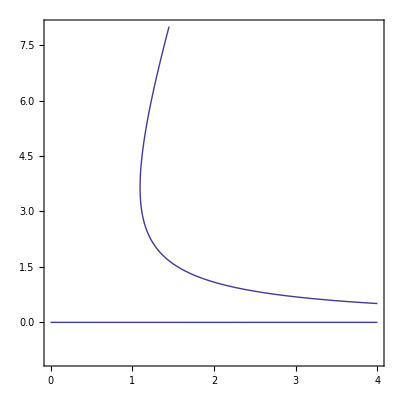

```mathematica
(* Plot bifurcation diagram: fixed points as function of parameter *)
ContourPlot[Evaluate[SSEqn],{F,0,4},{As,-1,8},PlotPoints -> 120]
```

```mathematica
(* Calculate bifurcation points *)
ss[[2,1]]
ss[[3,1]]
Flatten[Solve[0.66 (5F-2.236 √(-6+5 F^2))==0.66 (5 F+2.236 √(-6+5 F^2))]]
```

As→0.666667 (5. F-2.23607 √(-6.+5. F^2))

As→0.666667 (5. F+2.23607 √(-6.+5. F^2))

{F→-1.09545,F→1.09545}

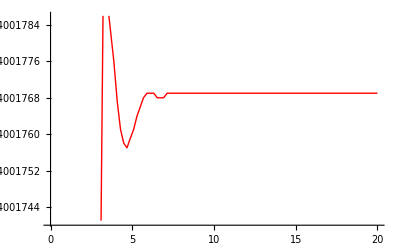

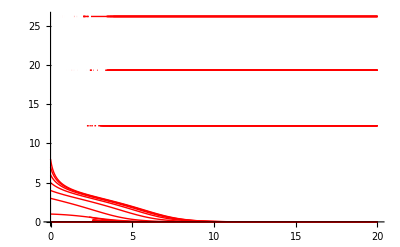

```mathematica
(* Transients *)
T=20;
ODEsol[F_,a_]:=NDSolve[{ODE[F,kb,kf,kd],A[0]==a},A[t],{t,0,T}]
ODETrajectory[F_,a_]:=Plot[Evaluate[A[t]/.ODEsol[F,a]],{t,0,T},PlotStyle -> Red]

Show[ODETrajectory[2,2]]
Show[Table[ODETrajectory[F,a],{F,0,4,1},{a,0,8,1}],PlotRange->All]
```

```mathematica
ParametricPlot[Evaluate[{A[t],A'[t]}/.ODEsol[2,3]],{t,0,T}]
```

-Graphics-